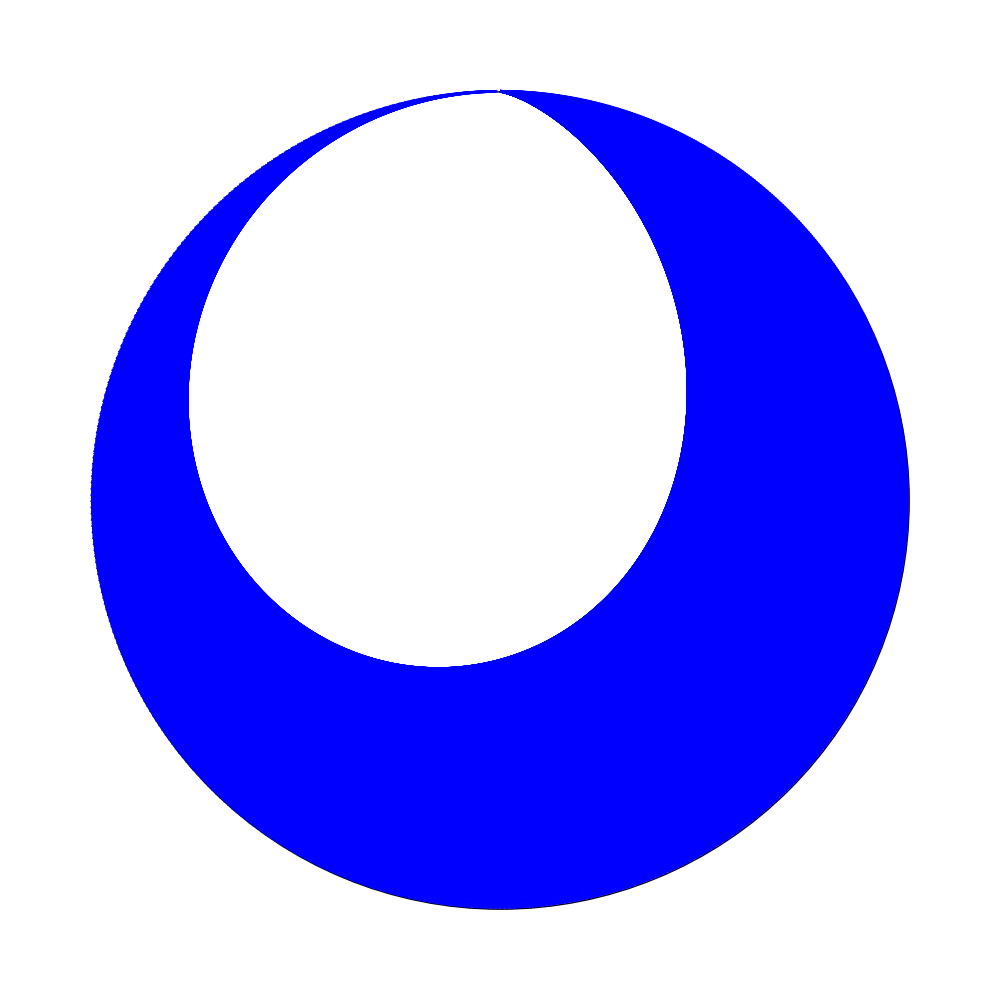

```mathematica
r[t_]:=(x=(Sin[2Pi t]);y=Cos[2Pi t];{x,y});
line[from_,to_]:=(
Style[Line[{r[from],r[ to]},VertexColors->{Yellow,Red}],Blue, Thickness[0.002]]
);

plot[fun_]:=(
Graphics[{Style[Circle[{0,0},1],Thickness[0.001]],Table[line[n, fun[n]],{n,0,1,1/2^10}]},ImageSize->1000]
);

plot[Function[n, n^3]]
```